Vícedimenzionální integrály

N dimenzí

Počet bodů, ve kterých vyčíslujeme funkční hodnotu roste s N -tou mocninou

Např. 30 bodů v jedné dimenzi, ve třech dimenzích počítáme funkci ve  30^3=2700 bodech

Metody výpočtu:

Snížení dimenze pomocí symetrie

Posloupnost opakovaných jednodimenzionálních integrací

Monte-Carlo

Metoda Monta Carlo

Integrační oblast V uzavřeme do co nejmenší oblasti se známým objemem V̄, ve které lze snadno generovat náhodné body

Vygenerujeme N náhodných bodů ve V̄ a vypočteme integrál ∫f(x⃗)ⅆV=(V̄)/N∑_(i=1)^N f̄(OverVector[x_i]), kde f̄(x⃗)=f(x⃗) pokud x⃗∈V, jinak  f̄(x⃗)=OverVector[0]

úkol 1. Metodou Monta Carlo určete velikost konstanty π

```mathematica
(* uvažujme kvadrant - kruhovou výseč vepsanou ve čtverci se stranou rovnou poloměru kruhu (viz gif ze složky 10-tého cvičení), v tom případě boudou jejich plochy v poměru π/4*)
r=0.;(* označíme r=red: body generované uvnitř kruhu*)
b=0.; (* označíme b=blue: body generované vně kruhu*)
n=5000;(* pčt iterací - vyzkoušejte různé hodnoty*)
listr={}; (*zde budeme ukládat červené body*)
listb={};(*zde budeme ukládat modré body*)
ploty={};(*zde budeme ukládat ploty pro tvorbu animace .gif*)
```

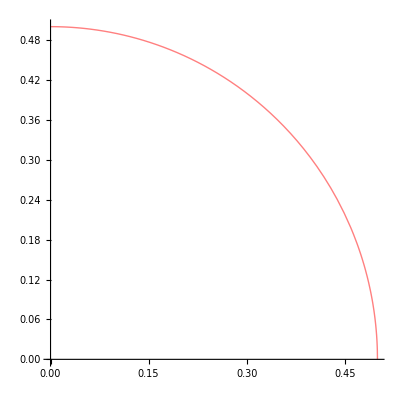

```mathematica
kruh=Plot[Sqrt[.25-x^2],{x,0,.5},AspectRatio->1,PlotStyle->{Thick, Pink}] (*čtvrtkruh - vykreslení*)
```

```mathematica
For[i=1,i<=n,i++,
xi=RandomReal[{0,.5},2]; (*generování 2 náhodných čísel v rozsahu (0,0.5)*)
If[xi[[1]]^2+xi[[2]]^2<=.25,
r=r+1;
AppendTo[listr,xi];,
b=b+1;
AppendTo[listb,xi];
];
pi=4*r/i; (*zkuste stejný kód spustit několikrát a porovnat získané hodnoty π pro stejné i různé n*)
If[i>4900,(* pokud je číslo iterace větší, než 4900, začnou se ukládat ploty pro tvorbu animace .gif do listu "ploty" - vykreslují se spolu s "kruh", pokud celkové množství plotů bude velké, je možné, že vytvoření animace bude trvat i několik minut*)
AppendTo[ploty,Show[{ListPlot[{listb,listr},PlotStyle->{Blue,Red},AspectRatio->1,Frame->True,FrameStyle->Directive[Gray,20],FrameLabel->{"odhad π je: " <>ToString[pi] },PlotLabel->Style["iterace "<>ToString[i] ,20],PlotMarkers->{Automatic,.008},ImageSize->Large],kruh}]
]
]
]
```

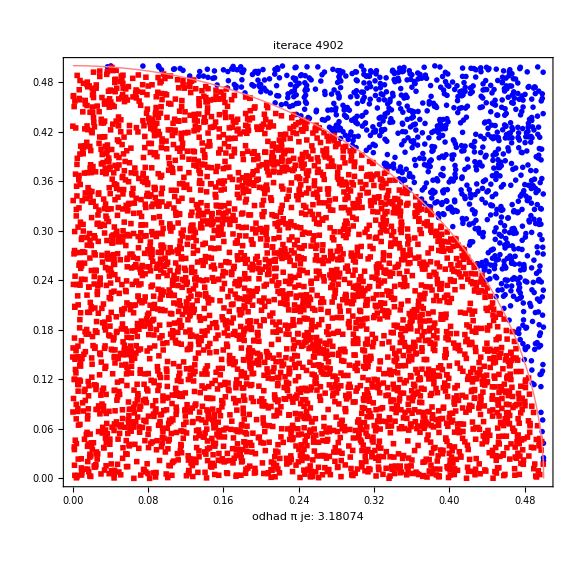

```mathematica
ploty[[2]]
```

```mathematica
Export["anim_m.gif",ploty,"DisplayDurations"->0.1] (*příkaz pro vytvoření animace, příkaz "DisplayDurations"->0.1 nastaví čas trvání jednoho snímku na 0.1 s*)
```